# Benchmarks for QDyn

All equations and calculations are in atomic units.

```mathematica
ℏ=1;
me=1;
```

## Imaginary - time dynamics

## Harmonic oscillator 1D

Harmonic oscillator with potential in form: 



Exact energies correspond to the following formula: 

ℏ

```mathematica
ω=0.1;
m = 1;
V=1/2*m*ω^2*x^2
```

0.005 x^2

### Energies for benchmark

```mathematica
Table[{n, ℏ*ω*(1/2+n)},{n,0,9}]//TableForm
```

0 | 0.05
1 | 0.15
2 | 0.25
3 | 0.35
4 | 0.45
5 | 0.55
6 | 0.65
7 | 0.75
8 | 0.85
9 | 0.95

```mathematica
Clear[ω,m,V]
```

## Morse potential 1D

Harmonic oscillator with potential in form: 



Exact energies correspond to the following formula: 



[Solution according to https://en.wikipedia.org/wiki/Morse_potential ]

This Morse potential should correspond to one of the states of the N2 molecule.

```mathematica
h=ℏ*2*Pi;
De=0.364;
re=2.041;
a=1.51;
m = 1834*28;
ν0=a/2/Pi*Sqrt[2*De/m];
V[r_]=De*(1-Exp[-a*(r-re)])^2-De
```

-0.364+0.364 (1-ⅇ^(-1.51 (-2.041+r)))^2

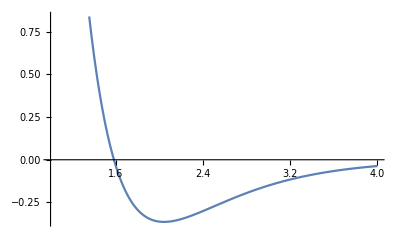

```mathematica
Plot[V[x],{x,1,4}]
```

### Energies for benchmark

```mathematica
Table[{n, h*ν0*(1/2+n)-(h*ν0*(1/2+n))^2/(4*De)-De},{n,0,9}]//TableForm
```

0 | -0.361163
1 | -0.355522
2 | -0.349925
3 | -0.344373
4 | -0.338865
5 | -0.333402
6 | -0.327983
7 | -0.322608
8 | -0.317278
9 | -0.311992

```mathematica
Clear[ν0,m,V,a,re,De,h]
```

## Harmonic oscillator 2D - symmetric

Harmonic oscillator with potential in form: 



Exact energies correspond to the following formula: 

ℏ

```mathematica
ωx=0.1; ωy=0.1;
m = 1;
V=1/2*m*ωx^2*x^2+1/2*m*ωy^2*y^2
```

0.005 x^2+0.005 y^2

### Energies for benchmark

```mathematica
data=Table[{nx,ny, ℏ*(ωx*(1/2+nx)+ ωy*(1/2+ny))},{nx,0,4}, {ny,0,4}]
```

{{{0,0,0.1},{0,1,0.2},{0,2,0.3},{0,3,0.4},{0,4,0.5}},{{1,0,0.2},{1,1,0.3},{1,2,0.4},{1,3,0.5},{1,4,0.6}},{{2,0,0.3},{2,1,0.4},{2,2,0.5},{2,3,0.6},{2,4,0.7}},{{3,0,0.4},{3,1,0.5},{3,2,0.6},{3,3,0.7},{3,4,0.8}},{{4,0,0.5},{4,1,0.6},{4,2,0.7},{4,3,0.8},{4,4,0.9}}}

```mathematica
Sort[ArrayReshape[data[[;;,;;,3]],5*5]][[;;10]] //TableForm
```

0.1
0.2
0.2
0.3
0.3
0.3
0.4
0.4
0.4
0.4

```mathematica
Clear[m,ωx,ωy,V,data]
```

## Harmonic oscillator 2D - asymmetric

Harmonic oscillator with potential in form: 



Exact energies correspond to the following formula: 

=ℏ

```mathematica
ωx=0.1; ωy=0.15;
m = 1;
V=1/2*m*ωx^2*x^2+1/2*m*ωy^2*y^2
```

0.005 x^2+0.01125 y^2

### Energies for benchmark

```mathematica
data=Table[{nx,ny, ℏ*(ωx*(1/2+nx)+ ωy*(1/2+ny))},{nx,0,4}, {ny,0,4}]
```

{{{0,0,0.125},{0,1,0.275},{0,2,0.425},{0,3,0.575},{0,4,0.725}},{{1,0,0.225},{1,1,0.375},{1,2,0.525},{1,3,0.675},{1,4,0.825}},{{2,0,0.325},{2,1,0.475},{2,2,0.625},{2,3,0.775},{2,4,0.925}},{{3,0,0.425},{3,1,0.575},{3,2,0.725},{3,3,0.875},{3,4,1.025}},{{4,0,0.525},{4,1,0.675},{4,2,0.825},{4,3,0.975},{4,4,1.125}}}

```mathematica
Sort[ArrayReshape[data[[;;,;;,3]],5*5]][[;;10]] //TableForm
```

0.125
0.225
0.275
0.325
0.375
0.425
0.425
0.475
0.525
0.525

```mathematica
Clear[m,ωx,ωy,V,data]
```

## Harmonic oscillator 3D - symmetric

Harmonic oscillator with potential in form: 



Exact energies correspond to the following formula: 

ℏ

```mathematica
ωx=0.1; ωy=0.1;ωz=0.1;
m = 1;
V=1/2*m*ωx^2*x^2+1/2*m*ωy^2*y^2+1/2*m*ωz^2*z^2
```

0.005 x^2+0.005 y^2+0.005 z^2

### Energies for benchmark

```mathematica
data=Table[{nx,ny,nz, ℏ*(ωx*(1/2+nx)+ ωy*(1/2+ny)+ ωz*(1/2+nz))},{nx,0,4}, {ny,0,4}, {nz,0,4}];
```

```mathematica
Sort[ArrayReshape[data[[;;,;;,;;,4]],5*5*5]][[;;10]] //TableForm
```

0.15
0.25
0.25
0.25
0.35
0.35
0.35
0.35
0.35
0.35

```mathematica
Clear[m,ωx,ωy,ωz,V,data]
```

## Harmonic oscillator 3D - asymmetric

Harmonic oscillator with potential in form: 



Exact energies correspond to the following formula: 

ℏ

```mathematica
ωx=0.1; ωy=0.07;ωz=0.13;
m = 1;
V=1/2*m*ωx^2*x^2+1/2*m*ωy^2*y^2+1/2*m*ωz^2*z^2
```

0.005 x^2+0.00245 y^2+0.00845 z^2

### Energies for benchmark

```mathematica
data=Table[{nx,ny,nz, ℏ*(ωx*(1/2+nx)+ ωy*(1/2+ny)+ ωz*(1/2+nz))},{nx,0,4}, {ny,0,4}, {nz,0,4}];
```

```mathematica
Sort[ArrayReshape[data[[;;,;;,;;,4]],5*5*5]][[;;10]] //TableForm
```

0.15
0.22
0.25
0.28
0.29
0.32
0.35
0.35
0.36
0.38

```mathematica
Clear[m,ωx,ωy,ωz,V,data]
```

## Real - time dynamics

## Harmonic oscillator 1D

Harmonic oscillator with potential in form: 



The initial wave function is considered as a gaussian function, for which the average position and momenta evolve according to Newton’s equations



The result is a harmonic motion .

```mathematica
ω=0.25;
m = 10;
V=1/2*m*ω^2*x^2
```

0.3125 x^2